# Lab 3 – Dynamics of regulatory and signalling pathways

Week 3: This week we will take a first look at dynamics of regulatory and signaling pathways in cells. Here you will go further with solving ODEs, a common approach to model molecular networks. We will infer reactions rates and signal response curves of for instance, positive and negative feedback loops. We will also briefly look at logical models.

## Background

Complex biomolecular systems can often not be reduced to elementary properties of individual components. Mathematical models that can explain and predict cellular functions are very useful to understand and engineer them. Continuous (quantitative) and discrete (qualitative) modelling are two of the main methods used today to model molecular and gene networks (a good review is given in the References list and will partly be the basis for the information given here).

Quantitative chemical kinetic models

Biochemical and cellular processes follow chemical and physical laws. If underlying chemical processes are know, the behaviour of a system can be described on the basis of thermodynamical and chemical kinetics (Le Novère, 2015). 
The most common approach to model molecular networks uses systems theory applied to chemical kinetics. Chemical kinetics uses the notion of processes where reactants are consumed and products are generated. The rate at which this process takes place is dependant on the quantity of the components involved, reaction order and parameters. The mathematical expression depends on the assumptions made.
The emergent behaviour of a given system is from the combination of all the processes affecting the components: values of the variables, e.g. protein amounts or gene activities, can be affected by processes such as binding, catalysis, degradation etc.. The resulting effect on a component will be the sum of the rates of all processes influencing the component, multiplied by the morphometrics of the processes. We will look at an example to explain this in more detail later on.

Parametrization of quantitative models

Suitable parameters, or rather the lack thereof, for building quantitative kinetic models is the bottleneck in using this modelling approach. One way to address this problem is to estimate the parameter values from experimental data sets. This estimation is a form of global optimization. We will look into parameter estimation and optimization later on in the course.

#### Linear and hyperbolic protein dynamicse example

Two simple examples of protein dynamics are shown in Figure 1: a. with linear structure: synthesis and degradation; b. with loop structure: phosphorylation and dephosphorylation reactions.  

-Graphics-
Figure 1. Two simple networks. S = Signal strength (e.g. concentration of mRNA), R = Responce element (e.g. protein concentration), RP = Phosphorylated responce element.  

Using the law of mass action, we can write the rate equations for both mechanisms. If we want to know the rate of change over time for the response we get:

	(a)	ⅆR/ⅆt= k_0+ k_1 S-k_2 R

	(b)	(ⅆ R_P)/ⅆt= k_1 S (R_T-R_P)-k_2 R_P, with R_T the total concentration of the response element: R_T= R_P+R

To look at the dynamics of these two systems, we need to solve them assuming steady-state (steady state solution). 
For each of the examples we will first plot the reaction rate as a function of R and a constant S. Then we will look at the signal-response curves.

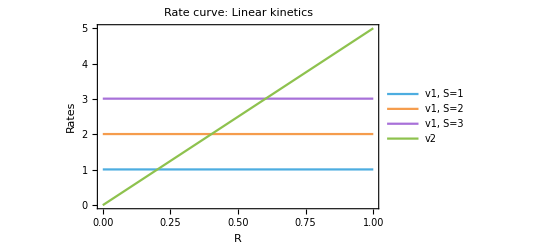

```mathematica
(*Define the functions and parameters, in this case k0 = 0.01, k1 = 1 and k2 = 5*)
paramsA = {k0-> 0.01,k1-> 1,k2-> 5};
rateqsA={v1->k0+k1 s,v2->k2 r};
(*Plot rates as a function of R at constant S*)
Plot[{
v1/.rateqsA/.paramsA/.s->1,
v1/.rateqsA/.paramsA/.s->2,
v1/.rateqsA/.paramsA/.s->3,
v2/.rateqsA/.paramsA},
{r,0,1},Frame->True,FrameLabel->{"R","Rates"}, 
PlotLegends -> {"v1, S=1", "v1, S=2", "v1, S=3", "v2"}, 
PlotLabel->Style["Rate curve: Linear kinetics", FontSize->18] , PlotTheme->"PastelColor"]
```

(k0+k1 s)/k2

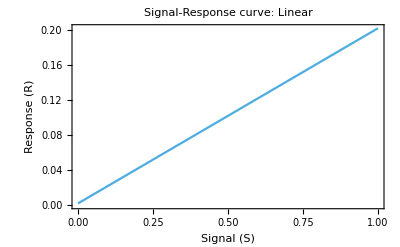

```mathematica
(*Find the steady state solution and then plot the signal-response curve*)
solA=Solve[0==(v1-v2)/.rateqsA,r][[1]][[1]][[2]]
Plot[solA/.paramsA,{s,0,1},Frame->True,FrameLabel->{"Signal (S)","Response (R)"}, PlotLabel->Style["Signal-Response curve: Linear", FontSize->18], PlotTheme->"PastelColor"]
```

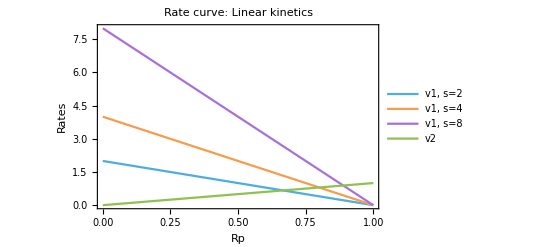

```mathematica
(*define the functions and parameters, in this case k1 = 1, k2 = 1 and the Subscript[R, T] = 1*)
rateqsB = {v1 ->k1 s (rt - rp), v2-> k2 rp} ;
paramsB = {k1 -> 1, k2 -> 1, rt -> 1};
Plot[{
v1/.rateqsB/.paramsB/.s->2,
v1/.rateqsB/.paramsB/.s->4,
v1/.rateqsB/.paramsB/.s->8,
v2/.rateqsB/.paramsB},
{rp,0,1},Frame->True,FrameLabel->{"Rp","Rates"}, 
PlotLegends-> {"v1, s=2", "v1, s=4", "v1, s=8", "v2"},
PlotLabel->Style["Rate curve: Linear kinetics", FontSize->18], PlotTheme->"PastelColor"]
```

(k1 rt s)/(k2+k1 s)

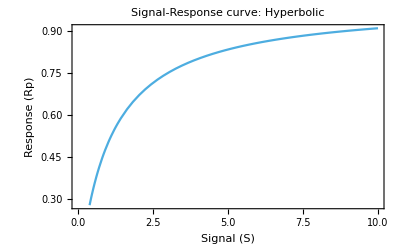

```mathematica
solB = Solve[0==(v1-v2)/.rateqsB,rp][[1]][[1]][[2]]
Plot[solB/.paramsB,{s,0,10}, Frame->True,FrameLabel->{"Signal (S)","Response (Rp)"}, PlotLabel->Style["Signal-Response curve: Hyperbolic", FontSize->18], PlotTheme->"PastelColor"]
```

#### Limitations of quantitative kinetic modelling

It is assumed in chemical kinetics that there is a homogeneous distribution of components in volumes. However, in reallity most signalling reactions have only a few components that are also heterogeneously located in spartially complex compartments. For gene regulation it is ever more so, since there are very few partners and the reactions take place on complex folded nucleic acid (DNA).

Qualitative logical modelling

Logic modelling is based on the notion that variables can take on a discrete number of states or values. The states of a variable is a logical combination of the states of other variables. In the most frequently used models, Boolean models, variables can have two values, 0 and 1. 
In most variants, time is not represented. State transitions take place at each time point, but a time step can represent different time durations for different transitions.

#### Logic model example

We can create a logic version of the following system, with two proteins A and B forming a complex AB, by building a model with three nodes and some added rules. 

The network
-Graphics-

Rules
- A(t+1) = 0 	if 	AB(t)
- A(t+1) = 1 	if 	NOT AB(t)
- B(t+1) = 0 	if 	NOT A(t) AND AB(t)
- B(t+1) = 1 	if 	(NOT A(t) AND NOT AB(t)) 	OR 	(A(t) AND AB(t))
- B(t+1) = 2 	if 	A(t) AND NOT AB(t)
- AB(t+1) = 0 	if 	NOT A(t) 			OR 	NOT B(t)
- AB(t+1) = 1 	if 	A(t) AND B(t)

The Boolean operators are in capital letters. The activity of A is inhibited by AB, otherwise it is always on. AB activity is stimulated when both A and B are active. Both A and AB are respresented by Boolean values (0 and 1). B’s activity has three values: it can be off when A is off and AB on, low when A and AB are off or A and AB are on, and high when A is on and AB off. 

The state-transition table of this network shows the input of the current state and the output of the next state.The state-transition table can be inferred from the rules and network graph. The number of states will be equal to the product of the number of activities of each node. In this case, protein A has 2 activities, B has 3 and AB has 2: 2*3*2 = 12.  

State-transition table
-Graphics-

With this information, it is possible to trace the trajectories across the ensembles of the states. 
The resulting state graph is a combination of all the trajectories. 

State-trasition graph
-Graphics-
From this graph you can see that whatever the starting state, the system will end up as a circular attractor in which the three variables will oscillate.

Mathematica doesn’t have a function to code the above example in an easy and neat way. This is mainly because of the non-Boolean value ( = 2) in this particular example. An example to code this (in a not very neat way) is given below.

```mathematica
(*Define the rules as above. For A = 0 -> a0, A = 1-> a1, ..., etc. *)
a0[A_,B_,AB_]:=If[Interpreter["Boolean"][AB],0]
a1[A_,B_,AB_]:=If[Not[Interpreter["Boolean"][AB]],1]
b0[A_,B_,AB_]:=If[Not[Interpreter["Boolean"][A]]&&Interpreter["Boolean"][AB],0]
b1[A_,B_,AB_]:=If[Not[Interpreter["Boolean"][A]]&&Not[Interpreter["Boolean"][AB]]||Interpreter["Boolean"][A]&&Interpreter["Boolean"][AB],1]
b2[A_,B_,AB_]:=If[Interpreter["Boolean"][A]&&Not[Interpreter["Boolean"][AB]],2]
ab0[A_,B_,AB_]:=If[Not[Interpreter["Boolean"][A]]||Not[Interpreter["Boolean"][B]],0]
ab1[A_,B_,AB_]:=If[Interpreter["Boolean"][A]&&Interpreter["Boolean"][B],1]

(*Null values are generated, which have to be set to the value zero*)
a[A_, B_, AB_]:=Apply[a0,{A, B, AB}]/.Null->0 + Apply[a1, {A, B, AB}]/.Null->0;
b[A_, B_, AB_]:=Apply[b0, {A, B, AB}]/.Null->0+Apply[b1, {A, B, AB}]/.Null->0+Apply[b2, {A, B, AB}]/.Null->0;
ab[A_, B_, AB_]:=Apply[ab0, {A, B, AB}]/.Null->0 + Apply[ab1,{A, B, AB}]/.Null->0;

(*Generate a list of all possible states*)
statesList = Tuples[{{0,1},{0,1,2},{0,1}}];

(*Apply the rules to this states list*)
listTransition = Catenate[{statesList//Transpose,{ Apply[a, statesList,1], Apply[b, statesList,1], Apply[ab, statesList,1]}}]//Transpose;

(*Make a nice readable table*)
TableForm[listTransition,TableHeadings->{Automatic,{"A(t)","B(t)","AB(t)","A(t+1)","B(t+1)","AB(t+1)"}},TableAlignments->Center]
```

| A(t) | B(t) | AB(t) | A(t+1) | B(t+1) | AB(t+1)
1 | 0 | 0 | 0 | 1 | 1 | 0
2 | 0 | 0 | 1 | 0 | 0 | 0
3 | 0 | 1 | 0 | 1 | 1 | 0
4 | 0 | 1 | 1 | 0 | 0 | 0
5 | 0 | 2 | 0 | 1 | 1 | 0
6 | 0 | 2 | 1 | 0 | 0 | 0
7 | 1 | 0 | 0 | 1 | 2 | 0
8 | 1 | 0 | 1 | 0 | 1 | 0
9 | 1 | 1 | 0 | 1 | 2 | 1
10 | 1 | 1 | 1 | 0 | 1 | 1
11 | 1 | 2 | 0 | 1 | 2 | 1
12 | 1 | 2 | 1 | 0 | 1 | 1

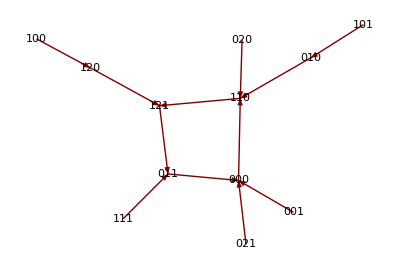

```mathematica
GraphPlot[{"000"->"110","001"->"000","010"->"110","011"-> "000","020"->"110","021"->"000","100"->"120","101"->"010","110"->"121","111"->"011","120"->"121","121"->"011"},DirectedEdges->True,VertexLabeling->All]
```

#### Limitations of logic models

Scaling of logical models is relativly easy, nonetheless the number of states increases exponentially with the number of variables. Additionally, the lack of time represented in the simple models makes it difficult to account for slow and fast processes and delays. 
Because of the purely qualitative nature of logical models, it can be difficult to choose between two behaviours proposed by logic modelling. For instance: functional negative feedback will always lead to periodic behavior, with the model cycling between states. With the quantitative kinetic model, it would lead to an equilibrium or an oscillation, depending on the feedback strength.

Interlude: Stability analysis

Biological systems can show different dynamic behaviours, ranging from stable to oscillating systems. We shall see this is more detail in the exercises. Let’s look a bit closer at stability analysis, because you can use this knowledge when analysing a system. 

If a system is at steady state, it should stay there, at least until an external perturbation occurs. Depending on the system’s behavior after perturbation, their steady states can be:

(a) stable (the system returns to this state)
(b) unstable (the system leaves this state) , or 
(c) metastable (the system behavior is indifferent)

To investigate whether a steady state of the ODE system is asymptotically stable, we need to linearize the system  and determine the eigenvalues of the Jacobian matrix. If the real parts of all eigenvalues are less than 0, i.e. negative (λ < 0), then the system is stable at that steady state. For two-dimensional systems, depending on the sign of the eigenvalues, the steady states (equilibrium points) can be distinguished:

- Node: Both eigenvalues are real and of same sign.
	- Stable: values are negative
	-Unstable: values are positive
-Saddle: Both eigenvalues are real and of opposite sign. Saddle point is always unstable. 
-Focus (or Spiral point): When the eigenvalues are complex conjugates. 
	-Stable: values are negative real part
	-Unstable: values are positive real part  
-Center: Both eigenvalues are pure imaginary. 

More (useful!!) info about equilibrium/matrices for equilibirum/stability analysis at: http://www.scholarpedia.org/article/Equilibrium
An extra file about stability analysis “Stability_Phase Plane.pdf” can be found on blackboard.

## Exercises

Analysing mathematical models of signal-response systems

-Graphics-
 : Network graphs of examples of a) perfect adaption, b) feedback 1, c) feedback 2 and d) feedback 3. Corresponding functions are given below.

In Figure 2, four networks are shown that each have a different dynamic behaviour. We will look at this behaviour by plotting for each network both the rate curves and signal-response curves.

A. Figure 2.a. shows a network for perfect adaption. This behaviour is typical of chemotactic systems that respond to an abrupt change in attractants or repellents and then adapt to a constant level of signal. Our sense of smell operates this way and therefore this type of response is also called a “Sniffer”. The kinetic equations for this system are given below. 

	ⅆR/ⅆt=k_1 S-k_2 X R,     with k_1=k_2=2,k_3=k_4=1
ⅆX/ⅆt=k_3 S-k_4 X

A.1. Plot both the rate curve of R as a function of R (with a constant value of S (S = 1, 2 and 3)) and the signal-response curve. Is it possible to plot a signal-response curve for this system? Explain this.

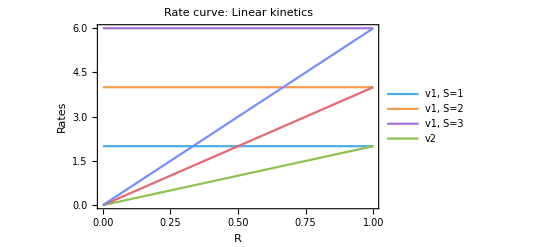

```mathematica
paramsA={k1->2,k2->2,k3->1,k4->1};
rateqsA={v1->k1*s,v2->k2*k3*s*r/k4};
(*Plot rates as a function of R at constant S*)
Plot[{v1/.rateqsA/.paramsA/.s->1,v1/.rateqsA/.paramsA/.s->2,v1/.rateqsA/.paramsA/.s->3,v2/.rateqsA/.paramsA/.s->1,v2/.rateqsA/.paramsA/.s->2,v2/.rateqsA/.paramsA/.s->3},{r,0,1},Frame->True,FrameLabel->{"R","Rates"},PlotLegends->{"v1, S=1","v1, S=2","v1, S=3","v2"},PlotLabel->Style["Rate curve: Linear kinetics",FontSize->18],PlotTheme->"PastelColor"]
```

(k1 k4)/(k2 k3)

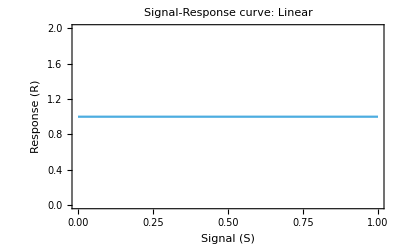

```mathematica
solA=Solve[0==(v1-v2)/.rateqsA,r][[1]][[1]][[2]]
Plot[solA/.paramsA,{s,0,1},Frame->True,FrameLabel->{"Signal (S)","Response (R)"}, PlotLabel->Style["Signal-Response curve: Linear", FontSize->18], PlotTheme->"PastelColor"]
```

A.2. Plot the concentrations of all the species over time (t = 0 - 20). S can be defined in incremental steps with values S  = 0, 1, 2, 3 and 4, each step lasting t = 4 (the Condition function (/;) can be very useful for this).

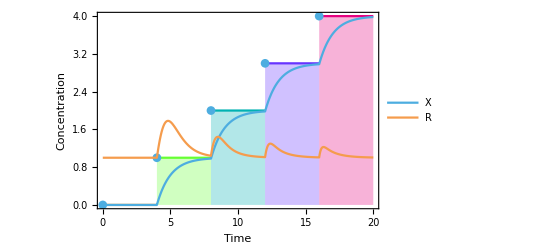

```mathematica
sss = Table[s,{s,0,20,4}];
natasjasIdea = {0,0,0,4,4,4,4,8,8,8,8,12,12,12,12,16,16,16,16,20,20,20,20};
natasjasIdea2 = {{0,0},{4,1},{8,2},{12,3},{16,4}};

(*Plot[Piecewise[{{0, t   <4}, {1, t<8}, {1, t<8}, {1, t<8}}], {t,0,20}
]*)

HelenaFavColor = "zalmroze" ;
(*Plot[Floor[t/4], {t,0,20}, PlotTheme->"Marketing"]
*)

solT[t_] = NDSolve[{r'[t] == 2*Floor[t/4] - 2 * x[t] * r[t], x'[t] == 1* Floor[t/4] - 1*x[t], r[0] == 1, x[0]== 0}, {r[t], x[t]}, {t,0,20}];

Show[ListStepPlot[natasjasIdea2, Joined->False, PlotTheme->"PastelColor", PlotMarkers->Automatic, ColorFunction->Function[{x,y},Hue[x]], Filling->Axis , Frame -> True,FrameLabel->{"Time", "Concentration"}, PlotLegends->"S"], 
Plot[Evaluate[{x[t]/. solT[t], r[t] /. solT[t]}],{t,0,20}, PlotTheme->"PastelColor", PlotLegends->{"X", "R"}]
]
```

B. In Figure 2.a. the signal influences the response via two pathways that push the response in opposite directions. This is an example also of feed-forward control. An alternative would be that the response pathway feeds back to the signal, which can be either positive, negative or mixed. 
From Figure 2.b. to 2.d. two types of positive feedback and one negative feedback example are given. In the negative feedback, the response R counteracts the effect of the stimulus S. In one type of  positive feedback, called mutual inhibition, the signal S enhances the synthesis of the response, which in turn inhibits E by phosphorylation. In this case E degrades R and therefore E and R are mutually antagonistic. In another type of positive feedback called mutual activation, the signal S enhances the synthesis of the response, which in turn enhances its own synthesis via phosphorylating E.
In the case of of this mutual activation example, the feedback can create a discontinuous switch. This means that the cellular response changes abruptly and irreversibly as the signal magnitude crosses a critical value S_crit. Between the values of S = 0 and S_crit, the system is called bistable. This is also called the one-way switch and they play major roles in developmental processes and cellular apoptosis, both characterized by a point-of-no-return. 
In the case of the mutual inhibition example, the feedback can create a toggle-switch. When S is decreased enough, the switch will go back to the off-state. Between the values S_crit1 < S < S_crit2, the response of the system can be small or large. The example of the negative feedback will cause a steady state concentration of the response R confined to a narrow window for a broad range of signal strengths. 

B.1.The following ODEs describe the three systems just explained. Analyze these systems by plotting the rate and signal-response curves.

Negative feedback: Homeostasis

	ⅆR/ⅆt=k_0 E(R)-k_2 S R
E(R)=G(k_3,k_4 R,J_3,J_4)  	with k_0 = 1, k_2= 1, k_3= 0.5, k_4= 1, J_3= J_4= 0.01. 

Take S = 0.5, 1 and 1.5.

Positive Feedback: Mutual inhibition

	ⅆR/ⅆt=k_0+k_1 S-k_2 R-k'_2 E(R) R
E(R)=G(k_3,k_4 R,J_3,J_4)		with k_0 = 0, k_1= 1, k_2= 0.05, k'_2= 0.5, k_3= 1, k_4= 0.2, J_3= J_4= 0.05.
	
Take S = 1, 1.5 and 2.

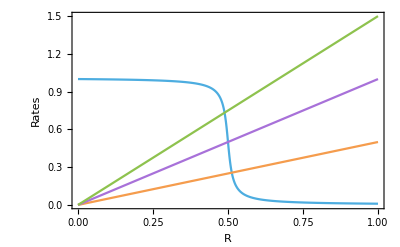

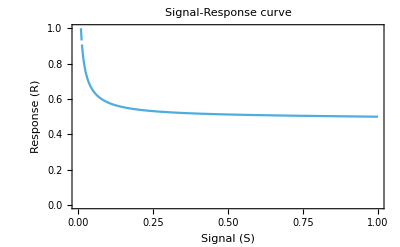

```mathematica
Remove[k0,k1,k2,k3,k4,J3,J4,s,r]

G[u_,v_,J_,K_]=2*u*K/(v-u+v*J+u*K+((v-u+v*J+u*K)^2-4*(v-u)*u*K)^0.5);

paramsHomeo={k0->1,k2->1,k3->0.5,k4->1,J3->0.01,J4->0.01};

equationsA={v1->k0*G[k3,k4*r,J3,J4], v2-> k2*s*r};

Plot[{v1/.equationsA/.paramsHomeo,v2/.equationsA/.paramsHomeo/.s->0.5,v2/.equationsA/.paramsHomeo/.s->1,v2/.equationsA/.paramsHomeo/.s->1.5},{r,0,1},PlotTheme->"PastelColor",Frame->True,FrameLabel->{"R","Rates"}]

(*solA=Solve[0==(v1-v2)/.rateqsA,r][[1]][[1]][[2]]
*)
solHomeo = Solve[0 == (v1-v2) /. equationsA,r][[1]][[1]][[2]];
Plot[solHomeo/.paramsHomeo,{s,0,1},Frame->True,FrameLabel->{"Signal (S)","Response (R)"},PlotRange-> {{0,1}, {0,1}},PlotLabel->Style["Signal-Response curve", FontSize->18], PlotTheme->"PastelColor"]
```

Positive Feedback Mutual activation

	ⅆR/ⅆt=k_0 E_p(R)+k_1 S-k_2 R
E_p(R)=G(k_3 R,k_4,J_3,J_4)	with k_0 = 0.4, k_1= 0.01, k_2= k_3= 1, k_4= 0.2, J_3= J_4= 0.05.
	 
Take S = 0, 8 and 16.

G refers to the Goldbeter-Koshland function and is defined as: 
	G(u,v,J,K)=(2u K)/(v-u+v J+u K+√((v - u + v J + u K)^2- 4(v-u)u K))

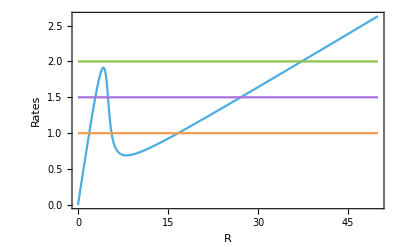

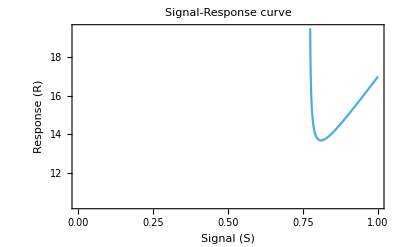

```mathematica
Remove[v1, v2, k0,k1,k2,k3,k4,J3,J4,s,r]
paramsInhibition={k0->0,k1->1,k2->0.05,k2b->0.5,k3->1,k4->0.2,J3->0.05,J4->0.05};
equationsB={v1-> k2*r+k2b*G[k3,k4*r,J3,J4]*r, v2->k0+k1*s};

Plot[{v1/.equationsB/.paramsInhibition, v2/.equationsB/.paramsInhibition/.s->1,v2/.equationsB/.paramsInhibition/.s->1.5,v2/.equationsB/.paramsInhibition/.s->2.0},{r,0,50},PlotTheme->"PastelColor", Frame->True,FrameLabel->{"R","Rates"}]

solInhibition = Solve[0 == (v1-v2) /. equationsB,r][[1]][[1]][[2]];
Plot[solInhibition/.paramsInhibition,{s,0,1},Frame->True,FrameLabel->{"Signal (S)","Response (R)"}, PlotLabel->Style["Signal-Response curve", FontSize->18], PlotTheme->"PastelColor"]
```

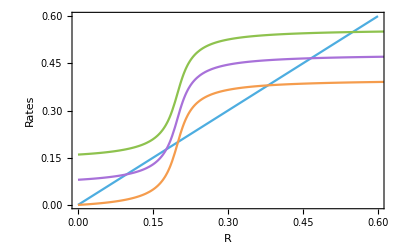

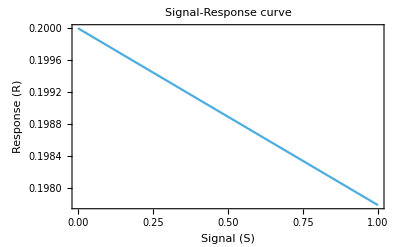

```mathematica
Remove[v1, v2, k0,k1,k2,k3,k4,J3,J4,s,r];

paramsActivation={k0->0.4,k1->0.01,k2->1,k3->1,k4->0.2,J3->0.05,J4->0.05};
equationsC={v2->k0*G[k3*r,k4,J3,J4]+k1*s, v1 -> k2*r};

Plot[{v1/.equationsC/.paramsActivation,v2/.equationsC/.paramsActivation/.s->0,v2/.equationsC/.paramsActivation/.s->8,v2/.equationsC/.paramsActivation/.s->16},{r,0,1},
PlotRange->{{0, 0.6},{0, 0.6}},PlotTheme->"PastelColor", Frame->True,FrameLabel->{"R","Rates"}]

solActivation = Solve[0 == (v1 - v2) /. equationsC,r][[1]][[1]][[2]];
Plot[solActivation/.paramsActivation,{s,0,1},Frame->True,FrameLabel->{"Signal (S)","Response (R)"}, 
PlotLabel->Style["Signal-Response curve", FontSize->18], PlotTheme->"PastelColor"]
```

B.1.a. Which network graphs given in Figure 2.b-d, and rate and signal-response curves belong to which feedback type? Explain what you based your choices on. 

B1.b. In the homeostatic system, explain why the response values are confined to a narrow window?

Case study: The Lac operon - A switch

An operon is a part of the DNA containing a cluster of genes controlled by a single promoter. If we take a closer look at the Lac-operon of Escherichia coli in Figure 3, we see the promoter which is repressed by a repressor in the absence of lactose. If lactose is available in the medium, import and conversion of lactose into allolactose occurs. Allolactose (A) is able to inhibit the inhibitor of the promoter and thereby allowing RNA polymerase to bind to the promoter and subsequently produce mRNA (M). The transcript contains information for the production of three enzymes: permease, β-galactosidase and transacetylase. The first two are respectively involved in cellular import of lactose and its enzymatic degradation, this mechanism is utilized by E. coli to derive energy from lactose.

-Graphics-
Figure 3: Schematic of the lac operon. The top scheme (a) shows the active repressor binding the operator in the absence of (allo)lactose, therefore inhibiting the transcription of the lac genes. Bottom scheme (b) shows deactivation of the repressor by allolactose, thereby deblocking the operator opening the way for the transcription of the lac genes.    

We assume that the production of mRNA is proportional to its translation into the proteins and we can thus write the following system of ODEs as discussed in (De Boer).

	ⅆM/ⅆt=k_1+k_2(1-1/(1 + A^n))-k_3 M
ⅆA/ⅆt=k_4 M L-k_5 A-V_max(M A)/(K_m + A)

A. Interpret all of the terms given in the two differential equations and describe both the positive and negative feedback loop.

B. Solve the ODEs with initial conditions M_0=0, A_0=0.05. Use the (arbitrary) parameter values k_1=0.05, k_2=k_3=L=V_max=k_4=1, k_5=0.2,K_m=2,n=5. 
Look at the mRNA concentration in steady-state, what happens if you increasing L from 1 to 3 with incrementing steps? What kind of system does this look like?

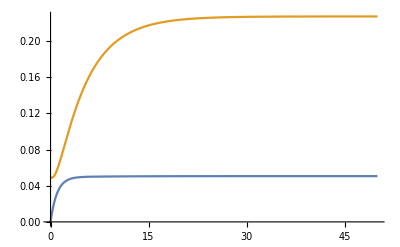

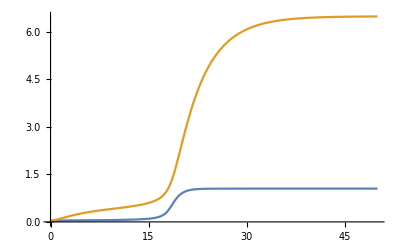

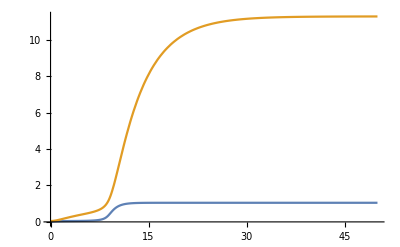

```mathematica
ClearAll["Global`*"]

k1 = 0.05;
k2 =  1;
k3 =  1;
L = 1;
Vmax =  1;
k4 =  1;
k5 = 0.2;
Km= 2;
n=5;

solved[t_] = NDSolve[{M'[t]== k1 + k2*(1- 1/(1+A[t]^n))-k3*M[t], A'[t]== k4*M[t]* L - k5*A[t]-Vmax*M[t]*A[t]/(Km+A[t]), M[0]==0, A[0]==0.05}, {M[t],A[t]}, {t, 0 ,50}];

L = 2;
solved2[t_] = NDSolve[{M'[t]== k1 + k2*(1- 1/(1+A[t]^n))-k3*M[t], A'[t]== k4*M[t]* L - k5*A[t]-Vmax*M[t]*A[t]/(Km+A[t]), M[0]==0, A[0]==0.05}, {M[t],A[t]}, {t, 0 ,50}];

L = 3;
solved3[t_] = NDSolve[{M'[t]== k1 + k2*(1- 1/(1+A[t]^n))-k3*M[t], A'[t]== k4*M[t]* L - k5*A[t]-Vmax*M[t]*A[t]/(Km+A[t]), M[0]==0, A[0]==0.05}, {M[t],A[t]}, {t, 0 ,50}];

Plot[{M[t]/.solved[t], A[t]/.solved[t]}, {t,0,50}]
Plot[{M[t]/.solved2[t], A[t]/.solved2[t]}, {t,0,50}]
Plot[{M[t]/.solved3[t], A[t]/.solved3[t]}, {t,0,50}]
```

C. One can derive curves, called isoclines, for which an ODE equals 0. This allows us to analyze the the qualitative behavior and easily identify points for which the system resides in a steady-state. 

C.a. Find the isoclines for mRNA in terms of the allolactose concentration for both equations and show them together with a StreamPlot (L = 1). 

C.b. Find the equilibrium points for this system (and check/compare them with the plot in C.a.), explain what kind of equilibrium points they are and then interpret these points biologically.

Simple boolean network

-Graphics-
The following simple Boolean network shows three components that influence each other. X and Z activate Y, Y activates Z, Z inactivates X and X can activate itself. Deactivating components will switch off the components they influence completely. Since there are only two values (on and off), the rules of this network can be easily inferred. 

A. Infer the rules for this network. 
B. Retrieve the state transition table. Unlike the example  in the introduction, this can be coded in a neater way. I would recommend inferring the graphs by hand and checking with the code (or vice versa). 
C. Draw the state transition graph. Explain what you see happening in this network, e.g. oscillations etc.

## References

- Le Novère, N., 2015. Quantitative and logic modelling of molecular and gene networks. Nature Reviews Genetics.
- De Boer, R.J. Ten Tusscher, k. Theoretical Biology. http://theory.bio.uu.nl/rdb/books/tb.pdf